0.1

(0.+166. q^2 | 0.1 | 0. | 0. | 0.
0.1 | 206.576+166. (-0.4+q)^2 | 0.1 | 0. | 0.
0. | 0.1 | 635.549+166. (-0.8+q)^2 | 0.1 | 0.
0. | 0. | 0.1 | 1303.34+166. (-1.2+q)^2 | 0.1
0. | 0. | 0. | 0.1 | 2294.94+166. (-1.6+q)^2)

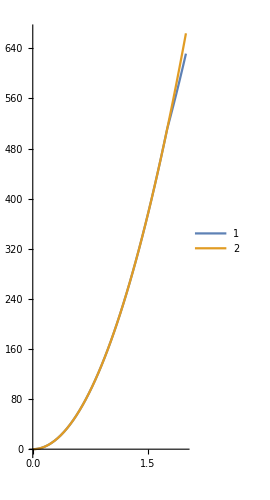

```mathematica
(*The energy landscape*)
ClearAll["Global`*"]
ene[q_,k_,q0_]:=.5*k*(q-q0)^2;
Q0={0,0.4,0.8,1.2,1.6};
V={0,206.576,635.549,1303.336,2294.939};
k=332;
c=0.1

self=ene[q,k,#]&/@Q0;
EneMat=DiagonalMatrix[self];
overlap={c,c,c,c};
Overlap1=DiagonalMatrix[overlap,1];
Overlap2=DiagonalMatrix[overlap,-1];
Vmat=DiagonalMatrix[V];
EneMatFinal=EneMat+Overlap1+Overlap2+Vmat;
EneMatFinal//MatrixForm
values=Eigenvalues[EneMatFinal];

(*Plot[{values[[1]],values[[2]],values[[3]],values[[4]],values[[5]]},{q,0,5},PlotRange->Full,AspectRatio->Full,PlotLegends->{"1","2","3","4","5"}]*)
Plot[{values[[1]],1/2*k*q^2},{q,0,2},PlotRange->Full,AspectRatio->Full,PlotLegends->{"1","2"}]
```

```mathematica
values
```

{Root[0.-2.41831×10^11 q^2+3.34036×10^11 q^3-4.3038×10^11 q^4+2.75558×10^11 q^5-1.50716×10^11 q^6+4.93543×10^10 q^7-1.36552×10^10 q^8+2.02489×10^9 q^9-2.53111×10^8 q^10+(1.45681×10^9-2.01227×10^9 q+4.20166×10^9 q^2-3.11702×10^9 q^3+2.27249×10^9 q^4-8.52911×10^8 q^5+2.94886×10^8 q^6-4.87925×10^7 q^7+7.62383×10^6 q^8) #1+(-9.69282×10^6+8.7773×10^6 q-1.10614×10^7 q^2+4.90287×10^6 q^3-2.356×10^6 q^4+440896. q^5-91853.3 q^6) #1^2+(17115.3-9372.95 q+8222.4 q^2-1770.67 q^3+553.333 q^4) #1^3+(-10.5165+2.66667 q-1.66667 q^2) #1^4+0.00200803 #1^5&,1],Root[0.-2.41831×10^11 q^2+3.34036×10^11 q^3-4.3038×10^11 q^4+2.75558×10^11 q^5-1.50716×10^11 q^6+4.93543×10^10 q^7-1.36552×10^10 q^8+2.02489×10^9 q^9-2.53111×10^8 q^10+(1.45681×10^9-2.01227×10^9 q+4.20166×10^9 q^2-3.11702×10^9 q^3+2.27249×10^9 q^4-8.52911×10^8 q^5+2.94886×10^8 q^6-4.87925×10^7 q^7+7.62383×10^6 q^8) #1+(-9.69282×10^6+8.7773×10^6 q-1.10614×10^7 q^2+4.90287×10^6 q^3-2.356×10^6 q^4+440896. q^5-91853.3 q^6) #1^2+(17115.3-9372.95 q+8222.4 q^2-1770.67 q^3+553.333 q^4) #1^3+(-10.5165+2.66667 q-1.66667 q^2) #1^4+0.00200803 #1^5&,2],Root[0.-2.41831×10^11 q^2+3.34036×10^11 q^3-4.3038×10^11 q^4+2.75558×10^11 q^5-1.50716×10^11 q^6+4.93543×10^10 q^7-1.36552×10^10 q^8+2.02489×10^9 q^9-2.53111×10^8 q^10+(1.45681×10^9-2.01227×10^9 q+4.20166×10^9 q^2-3.11702×10^9 q^3+2.27249×10^9 q^4-8.52911×10^8 q^5+2.94886×10^8 q^6-4.87925×10^7 q^7+7.62383×10^6 q^8) #1+(-9.69282×10^6+8.7773×10^6 q-1.10614×10^7 q^2+4.90287×10^6 q^3-2.356×10^6 q^4+440896. q^5-91853.3 q^6) #1^2+(17115.3-9372.95 q+8222.4 q^2-1770.67 q^3+553.333 q^4) #1^3+(-10.5165+2.66667 q-1.66667 q^2) #1^4+0.00200803 #1^5&,3],Root[0.-2.41831×10^11 q^2+3.34036×10^11 q^3-4.3038×10^11 q^4+2.75558×10^11 q^5-1.50716×10^11 q^6+4.93543×10^10 q^7-1.36552×10^10 q^8+2.02489×10^9 q^9-2.53111×10^8 q^10+(1.45681×10^9-2.01227×10^9 q+4.20166×10^9 q^2-3.11702×10^9 q^3+2.27249×10^9 q^4-8.52911×10^8 q^5+2.94886×10^8 q^6-4.87925×10^7 q^7+7.62383×10^6 q^8) #1+(-9.69282×10^6+8.7773×10^6 q-1.10614×10^7 q^2+4.90287×10^6 q^3-2.356×10^6 q^4+440896. q^5-91853.3 q^6) #1^2+(17115.3-9372.95 q+8222.4 q^2-1770.67 q^3+553.333 q^4) #1^3+(-10.5165+2.66667 q-1.66667 q^2) #1^4+0.00200803 #1^5&,4],Root[0.-2.41831×10^11 q^2+3.34036×10^11 q^3-4.3038×10^11 q^4+2.75558×10^11 q^5-1.50716×10^11 q^6+4.93543×10^10 q^7-1.36552×10^10 q^8+2.02489×10^9 q^9-2.53111×10^8 q^10+(1.45681×10^9-2.01227×10^9 q+4.20166×10^9 q^2-3.11702×10^9 q^3+2.27249×10^9 q^4-8.52911×10^8 q^5+2.94886×10^8 q^6-4.87925×10^7 q^7+7.62383×10^6 q^8) #1+(-9.69282×10^6+8.7773×10^6 q-1.10614×10^7 q^2+4.90287×10^6 q^3-2.356×10^6 q^4+440896. q^5-91853.3 q^6) #1^2+(17115.3-9372.95 q+8222.4 q^2-1770.67 q^3+553.333 q^4) #1^3+(-10.5165+2.66667 q-1.66667 q^2) #1^4+0.00200803 #1^5&,5]}